# Attempt to rewrite with arrays

```mathematica
correctP[0,i_,nopts_] := (1 - theta[i]) / Sum[1 - theta[k],{k,1,nopts}]
correctP[1,i_,nopts_] := (theta[i]) / Sum[theta[k],{k,1,nopts}]
correctPCum[y_,i_,nopts_]:= Sum[correctP[y,k,nopts],{k,1,i}]
q[y_,x_, phi_,nopts_] := Module[{phiCum,phiWrap},
	phiWrap[y2_,k2_]= If[k2 == nopts, 1 - Sum[phi[y2,i],{i,1,nopts-1}], phi[y2,k2]];
	phiCum[y3_,k3_] =Sum[phiWrap[y3,i],{i,1,k3}];
	Piecewise[Table[{
		correctPCum[y, k -1, nopts] + correctP[y,k, nopts]*(x - phiCum[y,k - 1])/phiWrap[y,k],
		phiCum[y, k - 1]<x ≤ phiCum[ y,k]
	},{k,1,nopts}]
]
]
pY[1,nopts_] := 1/nopts *Sum[theta[k],{k,1,nopts}]
pY[0,nopts_] := 1-pY[1, nopts]
sumQ[phi_,nopts_] := Sum[q[y,x,phi, nopts] * pY[y,nopts], {y,0,1}]

thetaCond[nopts_Integer] := 0 < theta[1] && (And @@ Table[ theta[k] < theta[k + 1], {k, 1, nopts - 1}]) && theta[nopts] < 1;
phiCond[nopts_Integer] := And @@ Flatten[Table[0 <phi[y,k] <1, {y,0,1},{k,1,nopts-1}]];

phiTarget[nopts_] := Flatten[Table[phi[y,k], {y,0,1}, {k, 1, nopts - 1}]]

(*
solvePhi[phi_,nopts_,subst_]:=Reduce[Resolve[ForAll[x,{0<x<1},sumQ[phi,nopts]==x]&&phiCond[nopts]&&thetaCond[nopts]/. subst],phiTarget[nopts]]
*)
solvePhi[phi_,nopts_, subst_,condx_,condrest_]:= Reduce[Resolve[
ForAll[x,{condx}, 
sumQ[phi, nopts] ==x] && phiCond[nopts] && thetaCond[nopts] && condrest/. subst
 ], 
phiTarget[nopts], Reals] 
solvePhi[phi_,nopts_, subst_,condx_]:= solvePhi[phi, nopts,subst,condx,True]
solvePhi[phi_,nopts_, subst_]:= solvePhi[phi, nopts,subst,{0 < x <1}]
solvePhi[phi_,nopts_] := solvePhi[phi, nopts, {}]
```

```mathematica
testCorrect[nopts_] := Module[{correctPNopts},
correctPNopts[y_,k_] := correctP[y,k,nopts];
{ Reduce[q[0,x,correctPNopts,nopts] ==x  && 0<x<1 && thetaCond[nopts]],
Reduce[q[1,x,correctPNopts,nopts] ==x  && 0<x<1 && thetaCond[nopts]]}
]
testCorrect[2]
testCorrect[3]
testCorrect[4]
```

{0<x<1&&0<theta[2]<1&&0<theta[1]<theta[2],0<x<1&&0<theta[2]<1&&0<theta[1]<theta[2]}

{0<x<1&&0<theta[3]<1&&0<theta[2]<theta[3]&&0<theta[1]<theta[2],0<x<1&&0<theta[3]<1&&0<theta[2]<theta[3]&&0<theta[1]<theta[2]}

{0<x<1&&0<theta[4]<1&&0<theta[3]<theta[4]&&0<theta[2]<theta[3]&&0<theta[1]<theta[2],0<x<1&&0<theta[4]<1&&0<theta[3]<theta[4]&&0<theta[2]<theta[3]&&0<theta[1]<theta[2]}

1/10

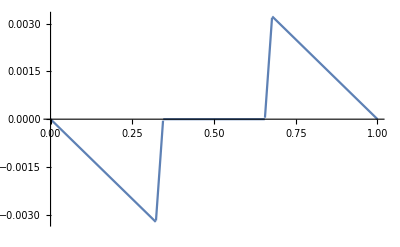

```mathematica
(*testECDF = sumQ[phi,2] /. {theta[1]->1/3,theta[2]->2/3, phi[0,1] -> 1/2*(1/2 + 2/3), phi[1,1] -> 1/2*(1/2 + 1/3)}*)
(*testECDF = sumQ[phi,2] /. {theta[1]->1/3,theta[2]->2/3, phi[0,1] -> 1/10, phi[1,1] -> 1/10}*)
a = 1/10
testECDF = sumQ[phi,3] /. {theta[1]->1/3,theta[2]->1/2, theta[3] -> 2/3, phi[0,1] -> (1 -a) *1/3 +a*4/9,phi[1,1] -> (1 - a) *1/3 +a *2/9,
phi[0,2] ->1/3, phi[1,2] -> 1/3};
Plot[testECDF - x,{x,0,1}]
```

```mathematica
solvePhi[phi, 2]
```

0<theta[2]<1&&0<theta[1]<theta[2]&&(phi[0,1]==1/2||phi[0,1]==(-1+theta[1])/(-2+theta[1]+theta[2]))&&phi[1,1]==(phi[0,1] theta[1])/(-1+2 phi[0,1]+theta[1])

```mathematica
(*solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3}]*)
```

```mathematica
subst={theta[1]->1/3,theta[2]->2/3};
Table[correctP[0,i,2], {i,1,2}] /. {subst}
Table[correctP[1,i,2], {i,1,2}] /. {subst}
Table[pY[y,2],{y, 0, 1}] /. {subst}
solvePhi[phi,2,subst]
```

{{2/3,1/3}}

{{1/3,2/3}}

{{1/2,1/2}}

(phi[0,1]==1/2&&phi[1,1]==1/2)||(phi[0,1]==2/3&&phi[1,1]==1/3)

```mathematica
q[0,x, phi, 2] /.subst
q[1,x, phi, 2] /.subst
FullSimplify[PiecewiseExpand[sumQ[phi,2]]] /.subst
```

Piecewise[{{(2 x)/(3 phi[0,1]), 0<x≤phi[0,1]}, {2/3+(x-phi[0,1])/(3 (1-phi[0,1])), phi[0,1]<x≤1}, {0, True}}]

Piecewise[{{x/(3 phi[1,1]), 0<x≤phi[1,1]}, {1/3+(2 (x-phi[1,1]))/(3 (1-phi[1,1])), phi[1,1]<x≤1}, {0, True}}]

Piecewise[{{1/2 x (2/(3 phi[0,1])+1/(3 phi[1,1])), x>0&&x≤phi[0,1]&&x≤phi[1,1]}, {1/2 (1/3+(2 x)/(3 phi[0,1])+(2 (-x+phi[1,1]))/(3 (-1+phi[1,1]))), 0<x≤1&&x≤phi[0,1]&&x>phi[1,1]}, {x/(3 phi[0,1]), x>0&&x≤phi[0,1]}, {1/2 ((-2/3-x/3+phi[0,1])/(-1+phi[0,1])+x/(3 phi[1,1])), x>phi[0,1]&&0<x≤1&&x≤phi[1,1]}, {-((2/3 (-1+x) (phi[0,1]-phi[1,1])+(1+x-2 phi[0,1]) (-1+phi[1,1]))/(2 (-1+phi[0,1]) (-1+phi[1,1]))), x≤1&&x>phi[0,1]&&x>phi[1,1]}, {(-2/3-x/3+phi[0,1])/(2 (-1+phi[0,1])), x>phi[0,1]&&x≤1}, {x/(6 phi[1,1]), x>0&&x≤phi[1,1]}, {1/2 (1/3+(2 (-x+phi[1,1]))/(3 (-1+phi[1,1]))), x>phi[1,1]&&x≤1}, {0, True}}]

```mathematica
(*res3 =solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3}]*)
(*solvePhi[phi,3]*)
```

$Aborted

```mathematica
Table[correctP[y,i,3], {y, 0, 1}, {i,1,2}] /. {theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3}
```

{{4/9,1/3},{2/9,1/3}}

```mathematica
res3 = Resolve[ForAll[x,{0<x<1}, sumQ[phi, 3] ==x] && phiCond[3] && thetaCond[3] /. {theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3}]
```

```mathematica
Reduce[And @@ Table[res3[[i]],{i, 1,10}], phiTarget[3]]
```

(phi[0,1]==1/3&&((phi[0,2]==1/3&&phi[1,1]==1/3&&phi[1,2]==1/3)||(phi[0,2]==2/5&&phi[1,1]==1/3&&phi[1,2]==2/7)))||(phi[0,1]==2/7&&phi[0,2]==3/14&&phi[1,1]==1/2&&phi[1,2]==3/14)||(phi[0,1]==8/21&&phi[0,2]==2/7&&phi[1,1]==4/15&&phi[1,2]==2/5)||(phi[0,1]==4/9&&phi[0,2]==1/3&&phi[1,1]==2/9&&phi[1,2]==1/3)||(phi[0,1]==1/2&&phi[0,2]==3/10&&phi[1,1]==1/5&&phi[1,2]==3/10)

```mathematica
(* Check the partial results - all 6 solutions seem to be OK *)
solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3, phi[0,1]-> 1/3, phi[0,2] -> 1/3}]
solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3, phi[0,1]-> 1/3, phi[0,2] -> 2/5}]
solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3, phi[0,1]-> 2/7, phi[0,2] -> 3/14}]
solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3, phi[0,1]-> 8/21, phi[0,2] -> 2/7}]
solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3, phi[0,1]-> 4/9, phi[0,2] -> 1/3}]
solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3, phi[0,1]-> 1/2, phi[0,2] -> 3/10}]
```

phi[1,1]==1/3&&phi[1,2]==1/3

phi[1,1]==1/3&&phi[1,2]==2/7

phi[1,1]==1/2&&phi[1,2]==3/14

phi[1,1]==4/15&&phi[1,2]==2/5

phi[1,1]==2/9&&phi[1,2]==1/3

phi[1,1]==1/5&&phi[1,2]==3/10

```mathematica
resOrdMin =solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3}, {0 < x <=phi[0,1] && x <= phi[1,1]}, True]
phi11subst = resOrdMin[[3]][[2]]
```

1/4<phi[0,1]<1&&0<phi[0,2]<1&&phi[1,1]==phi[0,1]/(-2+9 phi[0,1])&&0<phi[1,2]<1

phi[0,1]/(-2+9 phi[0,1])

```mathematica
Reduce[sumQ[phi, 3] ==x &&  x > Min[phi[0,1],phi[1,1]]&&0< x < Min[Max[ phi[0,1],phi[1,1]],phi[0,1] + phi[0,2], phi[1,1] + phi[1,2]] &&  phiCond[3] /. {theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3},x, Reals]
```

$Aborted

```mathematica
resOrd2 = solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3}, {x > Min[phi[0,1],phi[1,1]]&&0< x < Min[Max[ phi[0,1],phi[1,1]],phi[0,1] + phi[0,2], phi[1,1] + phi[1,2]]},True]
```

$Aborted

```mathematica
resOrdMax =solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3, phi[1,1]->phi11subst}, {phi[0,1] + phi[0,2]  < x <1 && phi[1,1] + phi[1,2] < x }, resOrdMin]
```

$Aborted

```mathematica
resOrdMax =solvePhi[phi,3,{theta[1] ->1/3 , theta[2]->1/2, theta[3]->2/3}, {phi[0,1] + phi[0,2]  < x <1 && phi[1,1] + phi[1,2] < x }, resOrdMin]
```

```mathematica
FullSimplify[sumQ[phi, 3] ==x && 0 < x <=phi[0,1] && x <= phi[1,1]]
FullSimplify[sumQ[phi, 3] ==x &&  x > Min[phi[0,1],phi[1,1]]&&0< x < Min[Max[ phi[0,1],phi[1,1]],phi[0,1] + phi[0,2], phi[1,1] + phi[1,2]] && x <= phi[1,1] &&  phi[0,2] > 0 && phi[1,2] >0]
FullSimplify[sumQ[phi, 3] ==x && phi[0,1] + phi[0,2]  < x <1 && phi[1,1] + phi[1,2] < x  && phi[0,2] > 0 && phi[1,2] >0]
```

x (3+(-1+theta[1])/phi[0,1])==(x theta[1])/phi[1,1]&&0<x≤phi[0,1]&&x≤phi[1,1]

-1+theta[1]+(-phi[0,1] (-1+theta[2])+x (-1+3 phi[0,2]+theta[2]))/phi[0,2]==(x theta[1])/phi[1,1]&&x>Min[phi[0,1],phi[1,1]]&&0<x<Min[phi[0,1]+phi[0,2],phi[1,1]]&&phi[1,2]>0

((-1+x) ((-2+3 phi[0,1]+3 phi[0,2]) (-1+phi[1,1]+phi[1,2])+(phi[0,1]+phi[0,2]-phi[1,1]-phi[1,2]) theta[3]))/((-1+phi[0,1]+phi[0,2]) (-1+phi[1,1]+phi[1,2]))==0&&phi[0,1]+phi[0,2]<x<1&&phi[1,1]+phi[1,2]<x&&phi[0,2]>0&&phi[1,2]>0